## GCode Converter

This notebook creates a very simple 3D implicit object, takes a slice of it, and converts the slice to GCode.

```mathematica
$Line = Infinity
```

∞

```mathematica
my3Dobject=(x-30)^2+(y-30)^2+(z-30)^2-200;
```

```mathematica
ContourPlot3D[my3Dobject==0,{x,0,50},{y,0,50},{z,0,50}]
```

-Graphics3D-

Now that I have my object, I want to take a slice to use for the line drawing. Slicing along one of the coordinate planes is really easy to do for Implicit Solid Models (this is not the case for b-rep polygonal models). Here I will slice using the plane parallel to the X-Y coordinate plane and passing through the point z=10.

```mathematica
slice=my3Dobject/.z->30
```

-200+(-30+x)^2+(-30+y)^2

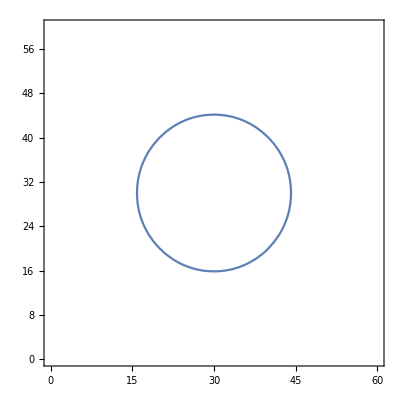

```mathematica
ContourPlot[slice==0,{x,0,60},{y,0,60}]
```

You may want to transform your object so the slice is reasonably large (units are mm in this plot), and in the first quadrant (x>0 and y>0) because otherwise the printer won’t be able to manufacture your design.

You will expand your modeller to 3D and then take a 2D slice. In this demo, I made the simpliest 3D implicit model I could think of, but you should implement transformations, primitives (at least sphere and box), and boolean operators like we did in the homework, and use it to construct something cool. Everything above this point should change!

When you are ready to convert a 2D shape into GCode, first do a RegionPlot. The following example includes some fun diagonal lines across the center of the shape to show what is “inside”. 
This image is exactly what we are going to turn into the gcode (except for the axes), in units of millimeters. You may want to scale your plot so it’s big enough to see on the printer.

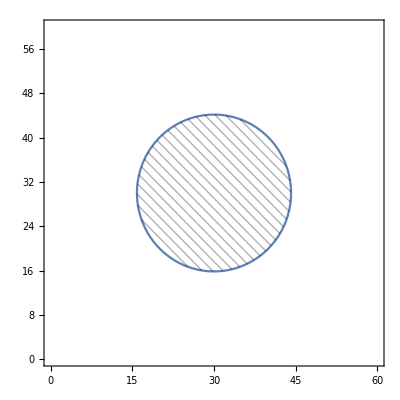

```mathematica
region =RegionPlot[slice≤ 0,{x,0,60},{y,0,60},
PlotStyle->None,Mesh->20,MeshFunctions->{#1+#2&}, (*These options control the hash fill*)
PlotPoints->30 (*This option controls how finely the plot resolves sharp corners*)
]
```

The following function takes some RegionPlot output and converts it into gcode to save to a file. In a minute, we’ll use this to create gcode from the plot above.

```mathematica
saveGCode[regionPlot_, fileName_]:=Module[{pointLocations, lineLists,lines,clean,gcodeLine,xycmds,zup,zdown,cmdlist,minrange,maxrange,bedsize},
(*Resource Functions*)
clean[n_]:=N[Chop[n,10^-5]];
gcodeLine[code_,x_,y_]:=ToString[StringForm["`` X`` Y``",code,clean[x],clean[y]]];
gcodeLine[code_,z_]:=ToString[StringForm["`` Z``",code,clean[z]]];
bedsize={200,200};


SetDirectory[NotebookDirectory[]];

pointLocations=Flatten[Cases[regionPlot,GraphicsComplex[x__,__]->x,∞],1];
minrange={Min[0,pointLocations[[;;,1]]],Min[0,pointLocations[[;;,2]]]}-3;
maxrange={Min[Max[pointLocations[[;;,1]]],bedsize[[1]]],Min[Max[pointLocations[[;;,2]]],bedsize[[2]]]}+3;
lineLists=Cases[regionPlot, Line[x__]->x,∞];
lines=pointLocations[[#]]&/@lineLists;

(*Generate GCode*)
xycmds=Map[gcodeLine["G01",#[[1]],#[[2]]]&,lines,{2}];
zup=gcodeLine["G00",5]<>"\n";
zdown=gcodeLine["G00",0];
cmdlist=Prepend[Flatten[Append[Insert[#,zdown,2],zup]&/@xycmds],zup];
Export[fileName,StringRiffle[cmdlist,"\n"],"Text"];

(*Produce a visualization*)
Legended[Graphics[Join[
Line/@lines,
{Green,PointSize[Large],Point[#[[1]]],Red,Point[#[[-1]]]}&/@lines,
{Blue,Dashed},Table[Line[{lines[[i,-1]],lines[[i+1,1]]}],{i,1,Length[lines]-1}],{EdgeForm[Directive[Orange,Thick]],Transparent,Rectangle[{0,0},bedsize]}
],PlotRange->{minrange,maxrange}ᵀ],Column[{LineLegend[{Black,Directive[Blue,Dashed],Directive[Orange,Thick]},{"Draw","Travel","Build Area"}],PointLegend[{Directive[Green,PointSize[Large]],Directive[Red,PointSize[Large]]},{"Pen Down", "Pen Up"}]}]]
];
```

Now we will use the function above to save our figure as a gcode file (in the same directory as the current notebook). The function also produces a visualization of the movement commands generated.

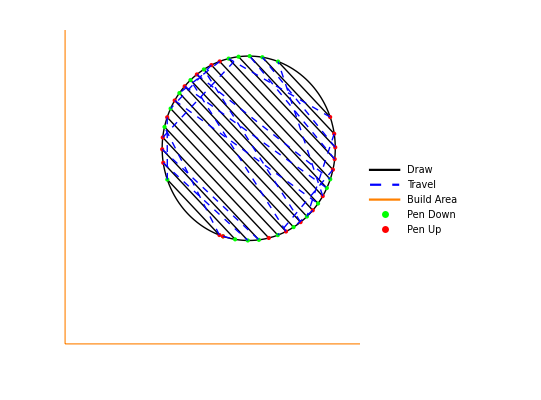

```mathematica
saveGCode[region,"test.gcode"]
```

Now there is a gcode file named “test.gc” in the same folder as this notebook, and the picture above shows what the gcode should produce. Be sure that your geometry is inside the orange rectangle (not all of which may be shown).

Copy the gcode file you produce to an SD card in the lab and go print it on the machine!